```mathematica
(* Convergence Tester: k sweep *)
(* Now, instead of computing single values and outputting a sequence for increasing m, 
we will do this repeateadly for increasing values of k, and then print a matrix. *)

(* ================ MACROS / USER PARAMETERS =================*)
(* f:= our function of m on S to be evaluated; 
k := offset for n. can be any integer so long as it doesn't bring n below 0.;
start:= first m to be checked in sequence. must be ≥ 1;
end:= last m to be checked in;
step := how much to increment by each iteration. determines what m are in our set S. 
e.g. step = 2 corresponds only even m.; *)

f0[m_] := Floor[(m*Sin[m]+2)/3]; (*converges to a(k) when function is positive*)
f00[m_] := Floor[(2*m*Sin[m]+2)/3]; (*does not converge to a(k), above m/2*)
f1[m_] := Ceiling[Abs[(m*Sin[m]+2)/3]];(*mark*)
f11[m_]:= Abs[(m*Sin[m]+2)/3];(*does not work, need rational for partition*)
f12[m_] := Floor[Abs[(m*Cos[m]+2)/3]];(*mark*)




start=12; 
end=108;
step = 12; (* Don't change this. *)
kstart = 1;
kend = 10;
kstep = 1;

(* ====================================================== *)
```

```mathematica
(* Dependencies: *)
(* 
	Name: partitionN
 Mathematical Notation: N(r,m,n)
 Desc.: Gives the number of partitions of a positive integer, n, whose RANK is congruent to r, modulo m. 
*)

partitionN[r_,m_,n_]:=Module[{r0=r,m0=m,n0=n,counter=0,i,rank,list},
	list = IntegerPartitions[n0];
	Do[rank=Max[list[[i]]]-Length[list[[i]]]; 
	If[Mod[rank,m0]==Mod[r0,m0],counter++]; ,{i,Length[list]}];
counter]
```

```mathematica
(* Build our matrix *)
mList = {};
For[i=kstart, i ≤ kend, i+=kstep, (* For each value of k *)
seq = {};
For[j = start, j ≤ end, j+=step,   (* For each value in our sequence *)
AppendTo[seq, partitionN[Abs[f00[j]],j,Abs[f00[j]]+i]]
];
AppendTo[mList,seq];
];
MatrixForm[mList]
```

(1 | 3 | 22 | 2 | 1 | 1 | 1 | 1040 | 479
0 | 2 | 24 | 0 | 0 | 0 | 0 | 1238 | 574
1 | 5 | 35 | 2 | 1 | 1 | 2 | 1508 | 709
1 | 5 | 42 | 2 | 1 | 1 | 1 | 1795 | 848
3 | 9 | 56 | 4 | 2 | 2 | 3 | 2169 | 1041
2 | 10 | 67 | 4 | 2 | 2 | 3 | 2575 | 1240
5 | 16 | 91 | 8 | 4 | 4 | 6 | 3098 | 1511
5 | 18 | 107 | 8 | 4 | 4 | 6 | 3663 | 1798
8 | 28 | 141 | 14 | 7 | 7 | 11 | 4384 | 2174
9 | 32 | 169 | 16 | 8 | 8 | 12 | 5177 | 2581)

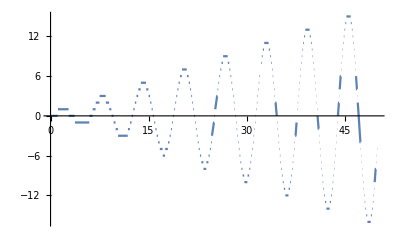

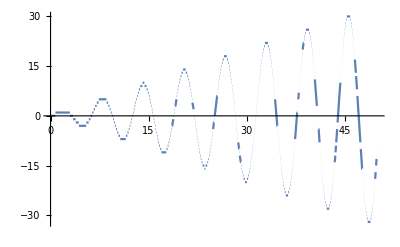

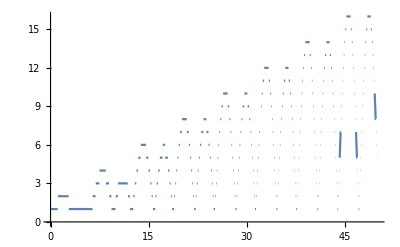

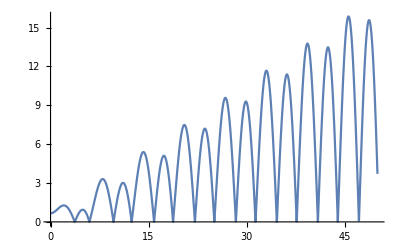

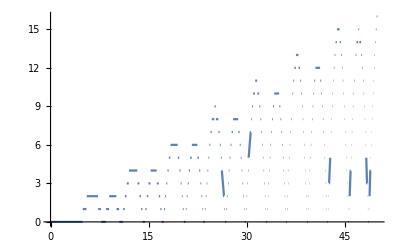

```mathematica
Plot[Floor[(m*Sin[m]+2)/3], {m, 0, 50}]
Plot[Floor[(2*m*Sin[m]+2)/3], {m, 0, 50}]
Plot[Ceiling[Abs[(m*Sin[m]+2)/3]], {m, 0, 50}]
Plot[Abs[(m*Sin[m]+2)/3], {m, 0, 50}]
Plot[Floor[Abs[(m*Cos[m]+2)/3]], {m, 0, 50}]
```